```mathematica
NormalizeData[symbol_,start_,end_]:=FinancialData[symbol,{start,end}]//Transpose@{#[[All,1]],#[[All,2]]/First@#[[All,2]]}&
WeightedMean[data_,weightList_]:=Total[weightList/Total@weightList*data]
RobustChart[symbols_,start_,end_,weightList_:Nothing]:=Module[{lists,allDates,associationLists,listsWithMissing,mean,weighted,data,table,ts,headings},
lists=NormalizeData[#,start,end]&/@symbols;
allDates=Table[#1&@@i,{stock,lists},{i,stock}]//Fold[Union,#]&;
associationLists=Table[#1->#2&@@i,{stock,lists},{i,stock}];
listsWithMissing=Table[Module[{association},
association=Association@a;
Table[k->association[k],{k,allDates}]],{a,associationLists}];
mean=Normal@Merge[listsWithMissing,Mean];
weighted=If[TrueQ[weightList==Nothing],Nothing,Normal@Merge[listsWithMissing,WeightedMean[#,weightList]&]];
data=listsWithMissing~Join~{mean,weighted};
table=Table[Select[Values@d,NumberQ]//{Last@#,StandardDeviation@#}&//{#1,#2,#1/#2}&@@#&,{d,data}];
ts=Transpose@{Keys@#,Values@#}&/@data;
headings=symbols~Join~{"Mean",If[TrueQ[weightList==Nothing],Nothing,"Weighted Mean"]};
TableForm@{DateListPlot[ts,PlotLegends->headings,PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All,PlotLabel->DateString@end],TableForm[table,TableHeadings->{headings,{"Return","Standard Deviation","Return/SD"}}]}
]
```

```mathematica
weights={5.5,5.42,4.96,4.77,4.55,4.38,3.69,3.49,3.37,2.99};
symbols={"AMZN","MSFT","V","BA","MA","JPM","CSCO","INTC","NFLX","ADBE"};
symbols2={"AMZN","MSFT","V","MA","NFLX","ADBE"};
start=DatePlus[Today,-Quantity[5, "Years"]];
end=Today;
```

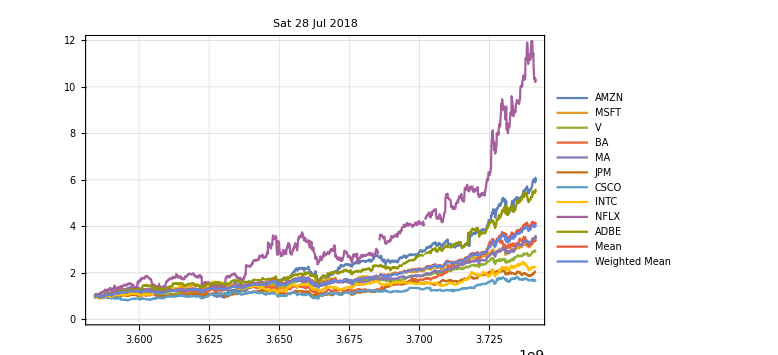
-Graphics-
 | Return | Standard Deviation | Return/SD
AMZN | 5.90657 | 1.27972 | 4.61552
MSFT | 3.47559 | 0.587792 | 5.91295
V | 2.96921 | 0.497378 | 5.96973
BA | 3.4283 | 0.683877 | 5.01303
MA | 3.47342 | 0.575742 | 6.03295
JPM | 2.06231 | 0.343349 | 6.00645
CSCO | 1.71852 | 0.238078 | 7.21829
INTC | 2.24441 | 0.325475 | 6.89578
NFLX | 10.3757 | 2.37844 | 4.3624
ADBE | 5.55289 | 1.1123 | 4.99226
Mean | 4.12069 | 0.787244 | 5.23432
Weighted Mean | 4.0117 | 0.760756 | 5.27331

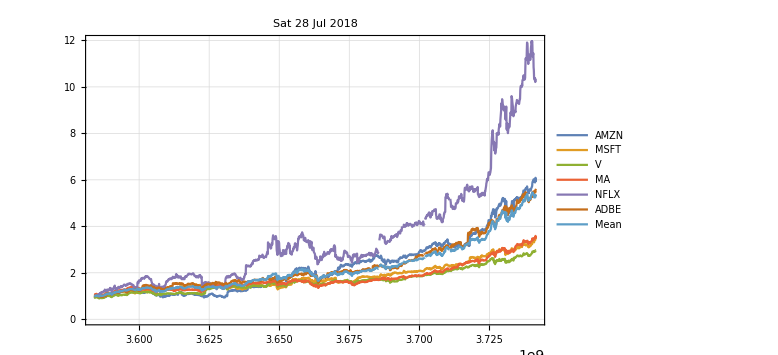
-Graphics-
 | Return | Standard Deviation | Return/SD
AMZN | 5.90657 | 1.27972 | 4.61552
MSFT | 3.47559 | 0.587792 | 5.91295
V | 2.96921 | 0.497378 | 5.96973
MA | 3.47342 | 0.575742 | 6.03295
NFLX | 10.3757 | 2.37844 | 4.3624
ADBE | 5.55289 | 1.1123 | 4.99226
Mean | 5.29223 | 1.06112 | 4.98742

```mathematica
RobustChart[symbols,start,end,weights]
RobustChart[symbols2,start,end]
```

```mathematica
PortfolioChart[stocks_,start_,end_]:=Module[{s,mean,data,symbols,std,return},
s=NormalizeData[#,start,end]&/@stocks;
mean=Transpose@{s[[1]][[All,1]],Mean/@Transpose@(#[[All,2]]&/@s)};
data=s~Join~{mean};
symbols=stocks~Join~{"mean"};
std=StandardDeviation@mean[[All,2]];
return=Last@mean[[All,2]];
TableForm@{DateListPlot[data,PlotLegends->symbols,PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All,PlotLabel->DateString@end],{return,std,return/std}//TableForm[#,TableHeadings->{{"Return","SD","Return/SD"},Automatic}]&}
]
```

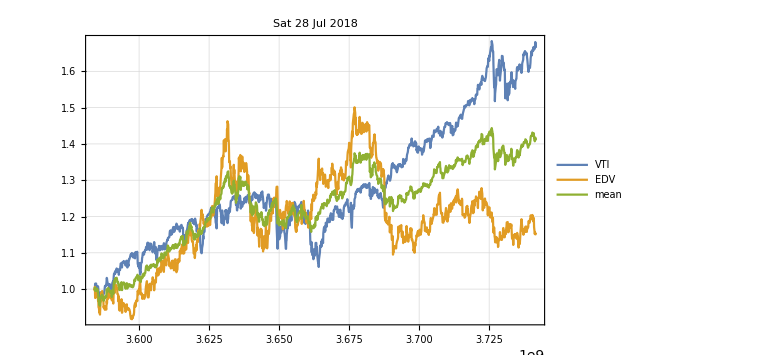
-Graphics-
Return | 1.40959
SD | 0.119416
Return/SD | 11.804

```mathematica
PortfolioChart[{"VTI","EDV"},start,end]
```

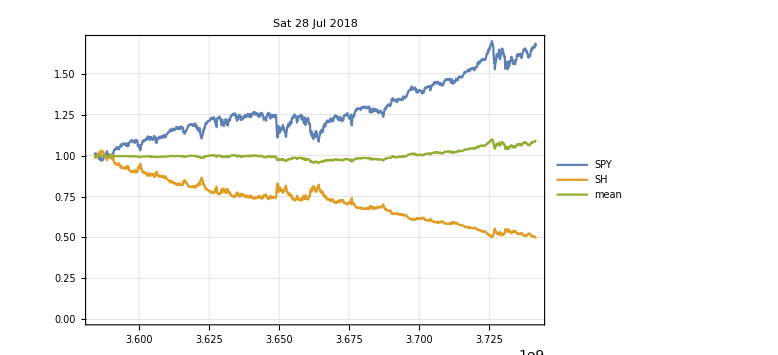
-Graphics-
Return | 1.08623
SD | 0.0297337
Return/SD | 36.5319

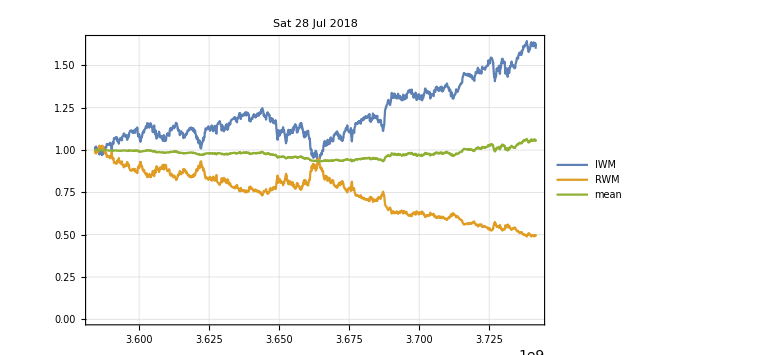
-Graphics-
Return | 1.05005
SD | 0.0269165
Return/SD | 39.0115

```mathematica
PortfolioChart[{"SPY","SH"},start,end]
PortfolioChart[{"IWM","RWM"},start,end]
```

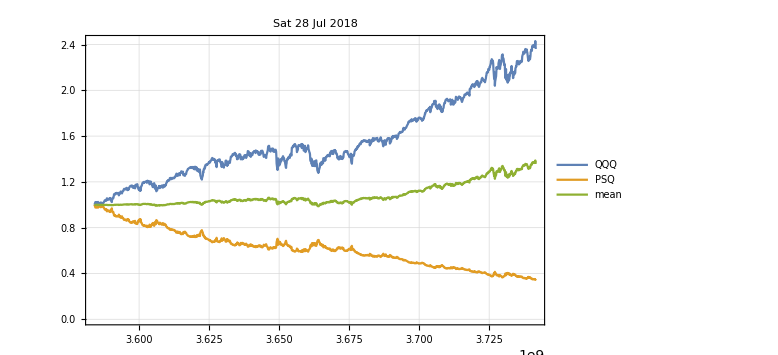
-Graphics-
Return | 1.35735
SD | 0.100294
Return/SD | 13.5336

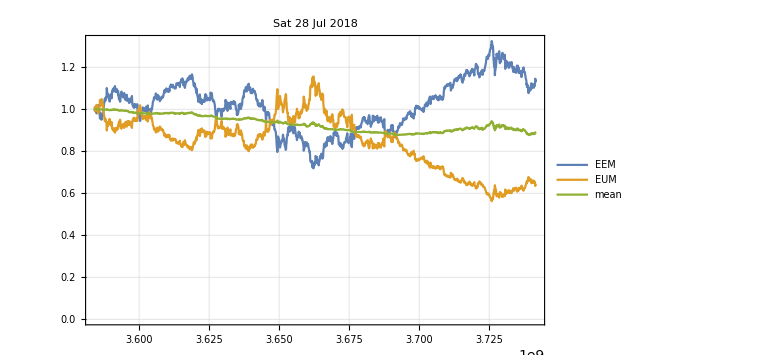
-Graphics-
Return | 0.888086
SD | 0.0384401
Return/SD | 23.1031

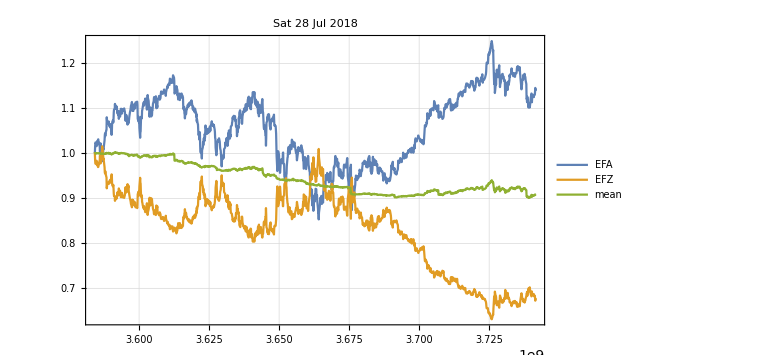
-Graphics-
Return | 0.909123
SD | 0.0331784
Return/SD | 27.4011

```mathematica
PortfolioChart[{"QQQ","PSQ"},start,end]
PortfolioChart[{"EEM","EUM"},start,end]
PortfolioChart[{"EFA","EFZ"},start,end]
```

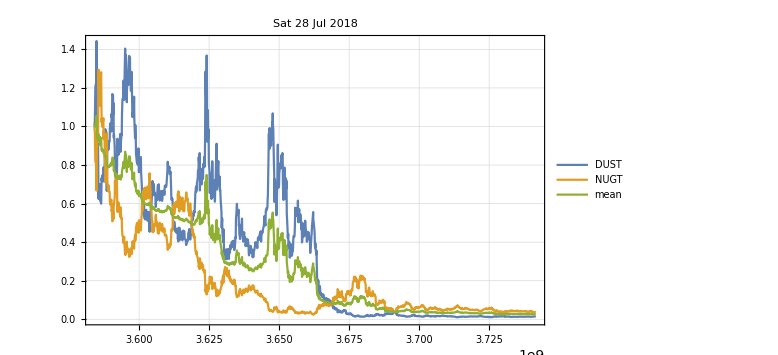
-Graphics-
Return | 0.0247696
SD | 0.264988
Return/SD | 0.0934745

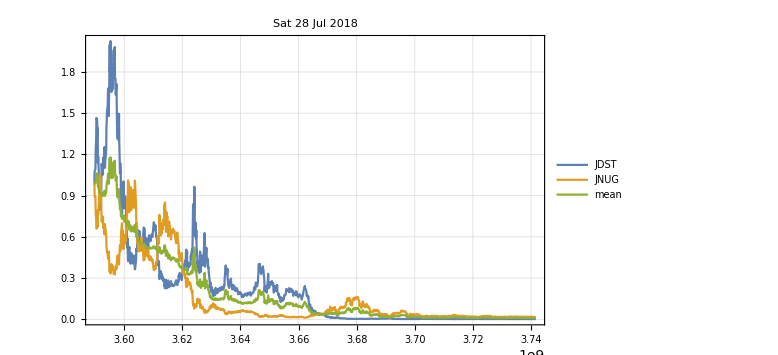
-Graphics-
Return | 0.00874565
SD | 0.270416
Return/SD | 0.0323415

```mathematica
PortfolioChart[{"DUST","NUGT"},start,end]
PortfolioChart[{"JDST","JNUG"},start,end]
```